```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Decay length of Neutral Pion

```mathematica
ReplaceAll[γ*β*τ/.γ->1/Sqrt[1-β^2],β->(√ϵ √(2 m+ϵ))/(m+ϵ)]//FullSimplify
```

```mathematica
piondecay=Convert[(√ϵ √(2 m+ϵ) τ)/(√(m^2/(m+ϵ)^2) (m+ϵ))*SpeedOfLight/.{τ->9*10^-17 Second,m->140 Mega ElectronVolt,ϵ->ϵ Mega ElectronVolt}//FullSimplify,Centimeter] 1/Centimeter;
```

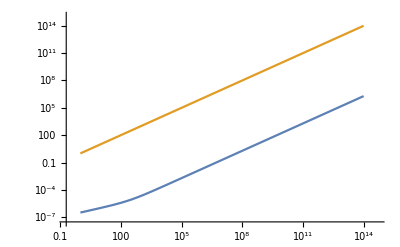

```mathematica
LogLogPlot[{piondecay,ϵ},{ϵ,1,10^14}]
```

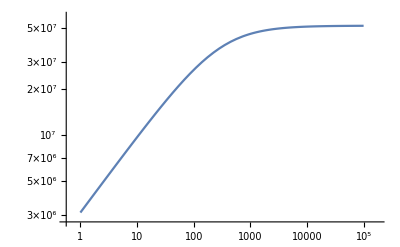

```mathematica
LogLogPlot[ϵ/piondecay,{ϵ,1,100000}]
```

```mathematica
piondecay/.ϵ->10
```

1.03785×10^-6

```mathematica
piondecay/.ϵ->1
```

3.23064×10^-7

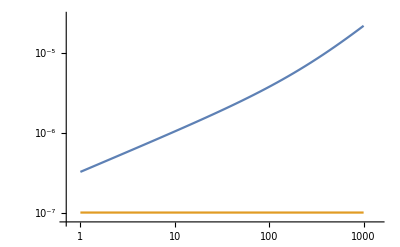

```mathematica
LogLogPlot[{piondecay,10^-7},{ϵ,1,10^3}]
```

```mathematica
Convert[1/(10^32 Centimeter^-3*100 Milli Barn),Centimeter]//N
```

1.×10^-7 Centimeter